## HW

### Do the Monte-Carlo simulation between beginning of 2013 and the end of 2015 of the market with 3 stocks such that {y_1{2013},y_2{2013},y_3{2013}}={100,120,78},with appreciation rates{a_1,a_2,a_3}={0.1,0.12,-0.5},with volatilities{Vol_1,Vol_2,Vol_3}={0.2,0.25,0.3},and correlarions ρ_(2,1)=.7,ρ_(3,1)=-.3,ρ_(3,2)=-.2.

```mathematica
A={{1,0,0},{Subscript[ρ, 2,1],Sqrt[1-Subscript[ρ, 2,1]^2],0},{Subscript[ρ, 3,1],x,y}};
```

```mathematica
A//TraditionalForm
```

(1 | 0 | 0
ρ_(2,1) | √(1-ρ_(2,1)^2) | 0
ρ_(3,1) | x | y)

```mathematica
A.Transpose[A]=={{1,Subscript[ρ, 2,1],Subscript[ρ, 3,1]},{Subscript[ρ, 2,1],1,Subscript[ρ, 3,2]},{Subscript[ρ, 3,1],Subscript[ρ, 3,2],1}}//TraditionalForm
```

(1 | ρ_(2,1) | ρ_(3,1)
ρ_(2,1) | 1 | √(1-ρ_(2,1)^2) x+ρ_(2,1) ρ_(3,1)
ρ_(3,1) | √(1-ρ_(2,1)^2) x+ρ_(2,1) ρ_(3,1) | x^2+y^2+ρ_(3,1)^2)==(1 | ρ_(2,1) | ρ_(3,1)
ρ_(2,1) | 1 | ρ_(3,2)
ρ_(3,1) | ρ_(3,2) | 1)

```mathematica
AA=A/.Solve[{√(1-Subscript[ρ, 2,1]^2) x+Subscript[ρ, 2,1] Subscript[ρ, 3,1]==Subscript[ρ, 3,2],x^2+y^2+Subscript[ρ, 3,1]^2==1},{x,y}][[2]]//Simplify
```

{{1,0,0},{ρ_(2,1),√(1-ρ_(2,1)^2),0},{ρ_(3,1),(-ρ_(2,1) ρ_(3,1)+ρ_(3,2))/(√(1-ρ_(2,1)^2)),√((-1+ρ_(2,1)^2+ρ_(3,1)^2-2 ρ_(2,1) ρ_(3,1) ρ_(3,2)+ρ_(3,2)^2)/(-1+ρ_(2,1)^2))}}

```mathematica
AA//TraditionalForm
```

(1 | 0 | 0
ρ_(2,1) | √(1-ρ_(2,1)^2) | 0
ρ_(3,1) | (ρ_(3,2)-ρ_(2,1) ρ_(3,1))/(√(1-ρ_(2,1)^2)) | √((ρ_(2,1)^2-2 ρ_(3,1) ρ_(3,2) ρ_(2,1)+ρ_(3,1)^2+ρ_(3,2)^2-1)/(ρ_(2,1)^2-1)))

```mathematica
cc={0.2,0.25,0.3}({{1, 0, 0}, {Subscript[ρ, 2,1], √(1-Subscript[ρ, 2,1]^2), 0}, {Subscript[ρ, 3,1], (Subscript[ρ, 3,2]-Subscript[ρ, 2,1] Subscript[ρ, 3,1])/(√(1-Subscript[ρ, 2,1]^2)), √((Subscript[ρ, 2,1]^2-2 Subscript[ρ, 3,1] Subscript[ρ, 3,2] Subscript[ρ, 2,1]+Subscript[ρ, 3,1]^2+Subscript[ρ, 3,2]^2-1)/(Subscript[ρ, 2,1]^2-1))}});
```

```mathematica
(cc.Transpose[cc])/(Transpose[{{0.2,0.25,0.3}}].{{0.2,0.25,0.3}})//Simplify
```

{{1.,0.+1. ρ_(2,1),0.+1. ρ_(3,1)},{0.+1. ρ_(2,1),1.,0.+1. ρ_(3,2)},{0.+1. ρ_(3,1),0.+1. ρ_(3,2),(-1.+1. ρ_(2,1)^2)/(-1.+ρ_(2,1)^2)}}

```mathematica
CC=cc/.{Subscript[ρ, 2,1]-> .7,Subscript[ρ, 3,1]-> -.3,Subscript[ρ, 3,2]-> -.2}
```

{{0.2,0.,0.},{0.175,0.178536,0.},{-0.09,0.00420084,0.286151}}

### PROF:

```mathematica
t0=2013;t1=2016;k=5000;y0={100,120,78};
𝕒={0.1,0.12,-0.5};
cc={0.2,0.25,0.3}({{1, 0, 0}, {Subscript[ρ, 2,1], √(1-Subscript[ρ, 2,1]^2), 0}, {Subscript[ρ, 3,1], (Subscript[ρ, 3,2]-Subscript[ρ, 2,1] Subscript[ρ, 3,1])/(√(1-Subscript[ρ, 2,1]^2)), √((Subscript[ρ, 2,1]^2-2 Subscript[ρ, 3,1] Subscript[ρ, 3,2] Subscript[ρ, 2,1]+Subscript[ρ, 3,1]^2+Subscript[ρ, 3,2]^2-1)/(Subscript[ρ, 2,1]^2-1))}});
CC=cc/.{Subscript[ρ, 2,1]-> .7,Subscript[ρ, 3,1]-> -.3,Subscript[ρ, 3,2]-> -.2};
```

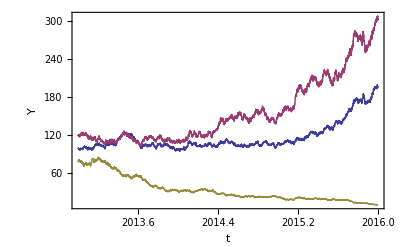

```mathematica
PROFMultiDimSDEsolver[{b_,c_,y0_},{t0_,t1_,k_}]:=
Module[{dt,dB,G},dt=(t1-t0)/k//N;
dB=Sqrt[dt]Table[Random[NormalDistribution[]],{k},{3}];
G[{t_,y_},dB_]:={t+dt,y+b[y] dt+c[y].dB};
FoldList[G,{t0,y0},dB]]
b[y_]:=y 𝕒
c[y_]:=y CC
PROFMultiTrajectory=PROFMultiDimSDEsolver[{b,c,y0},{t0,t1,5000}];
ST=Table[{#[[1]],#[[2,i]]}&/@PROFMultiTrajectory,{i,Length[𝕒]}];
ListPlot[ST,Frame->True,Joined-> True,FrameLabel->{t,Y},PlotRange->{0,All}]
```

```mathematica
MultiDimSDEsolver[{b_,c_,y0_},{t0_,t1_,k_}]:=Module[{m,dt,dB,G},m=Dimensions[c[y0]][[2]];dt=(t1-t0)/k//N;
dB=Sqrt[dt]Table[Random[NormalDistribution[]],{k},{m}];
G[{t_,y_},dB_]:={t+dt,y+b[y]dt+c[y].dB};
FoldList[G,{t0,y0},dB]]
```

### Mine

```mathematica
t0=2013;t1=2016;k=5000;y0={100,120,78};
𝕒={0.1,0.12,-0.5};
cc={0.2,0.25,0.3}({{1, 0, 0}, {Subscript[ρ, 2,1], √(1-Subscript[ρ, 2,1]^2), 0}, {Subscript[ρ, 3,1], (Subscript[ρ, 3,2]-Subscript[ρ, 2,1] Subscript[ρ, 3,1])/(√(1-Subscript[ρ, 2,1]^2)), √((Subscript[ρ, 2,1]^2-2 Subscript[ρ, 3,1] Subscript[ρ, 3,2] Subscript[ρ, 2,1]+Subscript[ρ, 3,1]^2+Subscript[ρ, 3,2]^2-1)/(Subscript[ρ, 2,1]^2-1))}});
CC=cc/.{Subscript[ρ, 2,1]-> .7,Subscript[ρ, 3,1]-> -.3,Subscript[ρ, 3,2]-> -.2};
```

```mathematica
MultiDimSDEsolver[{b_,c_,y0_},{t0_,t1_,k_}]:=
Module[{dt,dB,G},dt=(t1-t0)/k//N;
dB=Sqrt[dt]Table[Random[NormalDistribution[]],{k},{3}];
G[{t_,y_},dB_]:={t+dt,y+b [y]dt+c[y].dB};
FoldList[G,{t0,y0},dB]]
c[y_]:=y CC
b[y_]:=y 𝕒
```

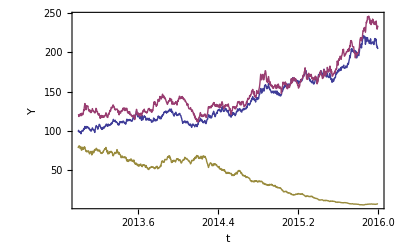

```mathematica
MultiTrajectory=MultiDimSDEsolver[{b,c,y0},{t0,t1,1000}];
ListPlot[Transpose[{Transpose[MultiTrajectory][[1]],#}]&/@Transpose[Transpose[MultiTrajectory][[2]]],Frame->True,Joined-> True,FrameLabel->{t,Y},PlotRange->{0,All}]
```

```mathematica
MultiTrajectory=MultiDimSDEsolver[{b,c,y0},{t0,t1,5}]
```

{{2013,{100,120,78}},{2013.6,{84.1407,74.5702,71.5272}},{2014.2,{77.8346,68.3453,50.3282}},{2014.8,{74.9899,75.2565,32.1667}},{2015.4,{73.4031,67.9916,12.2562}},{2016.,{93.2499,102.214,7.67928}}}

```mathematica
MultiTrajectory//TraditionalForm
```

(2013 | {100,120,78}
2013.6 | {84.1407,74.5702,71.5272}
2014.2 | {77.8346,68.3453,50.3282}
2014.8 | {74.9899,75.2565,32.1667}
2015.4 | {73.4031,67.9916,12.2562}
2016. | {93.2499,102.214,7.67928})

```mathematica
Transpose[MultiTrajectory][[1]]//TraditionalForm
```

{2013,2013.6,2014.2,2014.8,2015.4,2016.}

```mathematica
Transpose[Transpose[MultiTrajectory][[2]]]//TraditionalForm
```

(100 | 84.1407 | 77.8346 | 74.9899 | 73.4031 | 93.2499
120 | 74.5702 | 68.3453 | 75.2565 | 67.9916 | 102.214
78 | 71.5272 | 50.3282 | 32.1667 | 12.2562 | 7.67928)

```mathematica
Table[Transpose[{Transpose[MultiTrajectory][[1]],Transpose[Transpose[MultiTrajectory][[2]]][[i]]}],{i,3}]//TraditionalForm
```

({2013,100} | {2013.6,84.1407} | {2014.2,77.8346} | {2014.8,74.9899} | {2015.4,73.4031} | {2016.,93.2499}
{2013,120} | {2013.6,74.5702} | {2014.2,68.3453} | {2014.8,75.2565} | {2015.4,67.9916} | {2016.,102.214}
{2013,78} | {2013.6,71.5272} | {2014.2,50.3282} | {2014.8,32.1667} | {2015.4,12.2562} | {2016.,7.67928})

```mathematica
Transpose[{Transpose[MultiTrajectory][[1]],#}]&/@Transpose[Transpose[MultiTrajectory][[2]]]//TraditionalForm
```

({2013,100} | {2013.6,84.1407} | {2014.2,77.8346} | {2014.8,74.9899} | {2015.4,73.4031} | {2016.,93.2499}
{2013,120} | {2013.6,74.5702} | {2014.2,68.3453} | {2014.8,75.2565} | {2015.4,67.9916} | {2016.,102.214}
{2013,78} | {2013.6,71.5272} | {2014.2,50.3282} | {2014.8,32.1667} | {2015.4,12.2562} | {2016.,7.67928})

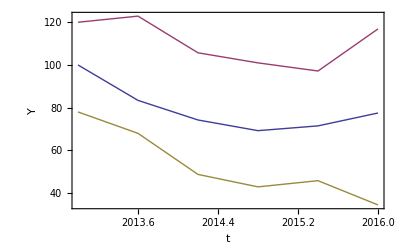

```mathematica
ListPlot[Transpose[{Transpose[MultiTrajectory][[1]],#}]&/@Transpose[Transpose[MultiTrajectory][[2]]],Frame->True,Joined->True,FrameLabel->{t,Y},PlotRange->{0,All}]
```